```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sasaki/Dropbox/@Res-SHARED/@OLIGOMORPH/Antigenic Escape and virulence/Antigen Escape and Virulence Evolution/Manusripts/-Source codes for figures/Figure 3/A Without cross immunity

### Expected ESS virulence

We expect that r(α)=β(α)-(u+γ+α), rather than R_0=β(α)/(u+γ+α) is maximized at ESS

With the tradeoff β(α)=c√α

```mathematica
Clear[R0,r,α,c,u,γ]
r[α_]=c Sqrt[α]-(u+γ+α);
R0[α_]=(c Sqrt[α])/(u+γ+α);
param={c->5,u->0.001,γ->0.5};
αESS=α/.Solve[D[r[α],α]==0,α]⟦1⟧
αESS0=α/.Solve[D[R0[α],α]==0,α]⟦1⟧
```

c^2/4

u+γ

wave speed

```mathematica
DIFFALF=0.01;
DIFFX = 0.01;
Simplify[r[αESS],Assumptions->c>0]
v=2Sqrt[(r[αESS]/.param)DIFFX]
```

1/4 (c^2-4 (u+γ))

0.479541

variance in virulence

```mathematica
Vα=c Sqrt[DIFFALF]/.param
```

0.5

total infected density

```mathematica
alpha=c^2/4/.param;
beta=c Sqrt[c^2/4]/.param;
gamma=γ/.param;
Ie=ℐ/.FindRoot[v(1- Exp[-beta ℐ/v])==(gamma+alpha)ℐ,{ℐ,.7}]
```

0.0533678

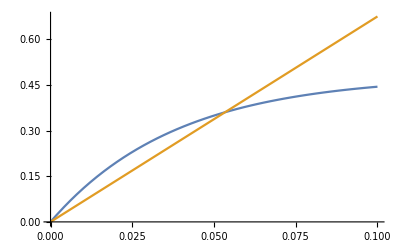

```mathematica
Plot[{v(1- Exp[-beta ℐ/v]),(gamma+alpha)ℐ},{ℐ,0,.1}]
```

```mathematica
Δx=100/2000//N
```

0.05

### Total density and mean traits

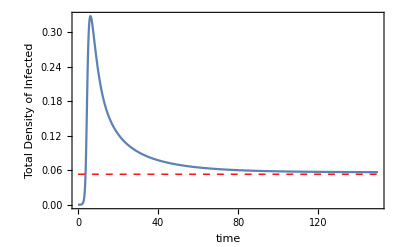

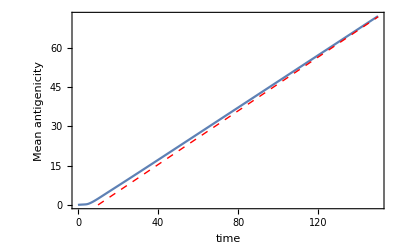

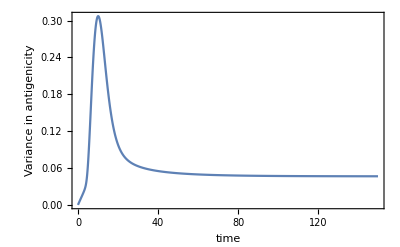

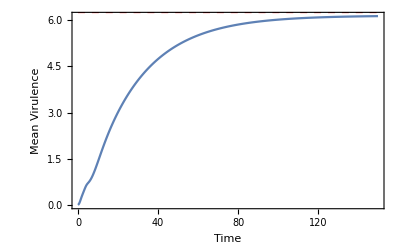

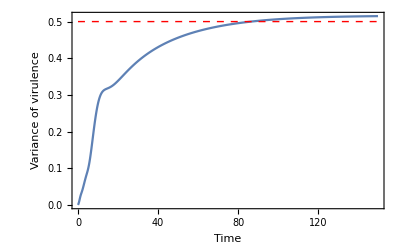

```mathematica
da = ReadList["dat/mean.d",Number,RecordLists->True];
{t,IT, ex, vx, ealf, valf} = Transpose[da];

ListLinePlot[Transpose[{t,Δx IT}],PlotRange->All,Frame->True,FrameLabel->{"time","Total Density of Infected"},Epilog->{Red,Dashed,Line[{{0,Ie},{150,Ie}}]}]

ListLinePlot[Transpose[{t,ex}],PlotRange->All,Frame->True,FrameLabel->{"time","Mean antigenicity"},Epilog->{Red,Dashed,Line[{{10,0},{150,v 150}}]}]

ListLinePlot[Transpose[{t,vx}],PlotRange->All,Frame->True,FrameLabel->{"time","Variance in antigenicity"}]

ListLinePlot[Transpose[{t,ealf}],PlotRange->All,Frame->True,FrameLabel->{"Time", "Mean Virulence"},Epilog->{Red,Dashed,Line[{{0,αESS/.param},{150,αESS/.param}}]}]

ListLinePlot[Transpose[{t,valf}],PlotRange->All,Frame->True,FrameLabel->{"Time","Variance of virulence"},Epilog->{Red,Dashed,Line[{{0,Vα},{150,Vα}}]}]
```

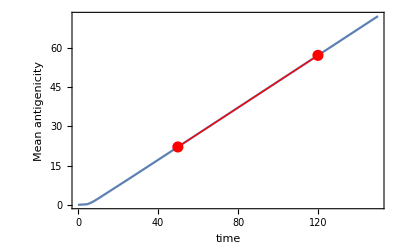

0.500086

```mathematica
ListLinePlot[Transpose[{t,ex}],PlotRange->All,Frame->True,FrameLabel->{"time","Mean antigenicity"},Epilog->{PointSize[0.02],Red,Point[{t⟦500⟧,ex⟦500⟧}],Point[{t⟦1200⟧,ex⟦1200⟧}],Line[{{t⟦500⟧,ex⟦500⟧},{t⟦1200⟧,ex⟦1200⟧}}]}]
speed=(ex⟦1200⟧-ex⟦500⟧)/(t⟦1200⟧-t⟦500⟧)
```

### Marginal distribution : antigenicity

```mathematica
da = ReadList["dat/marginal-x.d",Number,RecordLists->True];
{t, x,Ix} = Transpose[da];
t=Union[t];
x=Union[x];
Ix=Partition[Ix,Length[x]];
grfA=ListContourPlot[Transpose[Ix^0.2],PlotRange->All,ColorFunction->(GrayLevel[(1-#)]&),
DataRange->
{{Min[t],Max[t]},{Min[x],Max[x]}},
FrameLabel->{"time, t","antigenicity, x"},Epilog->{Red,Thick,Line[{{10,0},{150,v 150}}]}]
```

-Graphics-

### Marginal distribution : virulence

```mathematica
da = ReadList["dat/marginal-a.d",Number,RecordLists->True];
{t, alf,Ia} = Transpose[da];
t=Union[t];
alf=Union[alf];
Ia=Partition[Ia,Length[alf]];
ListContourPlot[Transpose[Ia^0.2],PlotRange->All,ColorFunction->(GrayLevel[(1-#)]&),
DataRange->{{Min[t],Max[t]},{Min[alf],Max[alf]}},FrameLabel->{"time, t","virulence, α"}]
```

-Graphics-

```mathematica
dat =Select[da, (#⟦2⟧<10)&];
{t, alf,Ia} = Transpose[dat];
t=Union[t];
alf=Union[alf];
Ia=Partition[Ia,Length[alf]];
evolalf=ListContourPlot[Transpose[Ia^0.2],PlotRange->All,ColorFunction->(GrayLevel[(1-#)]&),
DataRange->{{Min[t],Max[t]},{Min[alf],Max[alf]}},FrameLabel->{"time, t","virulence, α"}]
```

-Graphics-

```mathematica
grfB=Show[
Show[evolalf],
Graphics[{Red,Thick,Dashed,Line[{{0,αESS},{150,αESS}}/.param]}],
Graphics[{Blue,Thick,Dashed,Line[{{0,αESS0},{150,αESS0}}/.param]}]
]
```

-Graphics-

## Save file : Figure 1

### Save in Figure directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sasaki/Dropbox/@Res-SHARED/@OLIGOMORPH/Antigenic Escape and virulence/Antigen Escape and Virulence Evolution/Manusripts/-Source codes for figures/Figure 3/A Without cross immunity

### Time change in virulence distribution

```mathematica
FIGDIR="fig/";
```

```mathematica
Export[FIGDIR<>"EvolVirulenceWEscape-SIG0-TradeoffC5.eps",grfA];
```

```mathematica
Export[FIGDIR<>"EvolVirulenceWEscape-SIG0-TradeoffC5.pdf",grfA];
```

### Time change in antigenicity distribution

```mathematica
Export[FIGDIR<>"EvolAntigenicity-SIG0-TradeoffC5.eps",grfB];
```

```mathematica
Export[FIGDIR<>"EvolAntigenicity-SIG0-TradeoffC5.pdf",grfB];
```